# 1. Estimations of ϵ_1 and ϵ_2 appeared in Eq.(5)

Defining a function to calculate ϵ_1 and  ϵ_2

```mathematica
Ratio[f1val_,prec_:40]:=Block[{f1=SetPrecision[f1val,prec+10],Msun,c,G,Mchirp,Mtot,Dist,offset,f0,t0,fISCO,f1r,te,ve,R,Iexact1,Iapprox1,Iexact2,Iapprox2,ϵ1,ϵ2},
(Msun=2*10^30;
c=3*10^8;
G=6.67*10^-11;
Mchirp=1.19*Msun ;
Mtot=2.82*Msun ;
Dist= 1.2*10^24 ;
f0=20;
t0=165;
       offset=N[-t0-Dist/c];
fISCO=1593;
te[f_]=N[(-5π*Mchirp^2)/(256*(π*Mchirp)^(11/3))*c^5/G^(5/3)*(f^(-8/3)-f0^(-8/3))+offset];
        ve[f_]=N[(π*G*Mtot*f)^(1/3)];
R[f_]=ve[f]/(2 π f);
f1r=f1*fISCO;
   Iexact1=NIntegrate[R[f]*Sin[2π*f*te[f]]-R[f0]*Sin[2π*f0*te[f0]],{f,f0,f1r}];
        Iapprox1=NIntegrate[2/π*Sqrt[(R[f]^2+R[f0]^2)/2],{f,f0,f1r}];
ϵ1=Iexact1/Iapprox1;
Iexact2=NIntegrate[ve[f]*Cos[2π*f*te[f]]-ve[f0]*Cos[2π*f0*te[f0]],{f,f0,f1r}];
        Iapprox2=NIntegrate[2/π*Sqrt[(ve[f]^2+ve[f0]^2)/2],{f,f0,f1r}];
        ϵ2=-Iexact2/Iapprox2;
        {ϵ1,ϵ2}

)];(* Ratios of the exact integrals and approx integrals. Data are taken from the website https://en.wikipedia.org/wiki/GW170817 *)
```

```mathematica
ϵ1List=Table[{f1val,Ratio[f1val][[1]]},{f1val,.1,1,.1}];
```

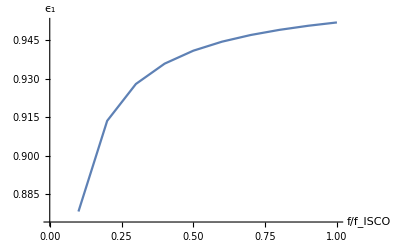

```mathematica
ListPlot[ϵ1List,Joined->True,AxesLabel->{"f/f_ISCO","ϵ_1"}]
```

```mathematica
ϵ2List=Table[{f1val,Ratio[f1val][[2]]},{f1val,.1,1,.1}];
```

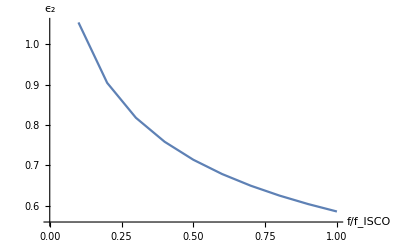

```mathematica
ListPlot[ϵ2List,Joined->True,AxesLabel->{"f/f_ISCO","ϵ_2"}]
```

As it is clear from the list/plot that ϵ_(1,2) , i.e., the ratios of  the exact results and our approximated results are always order unity positive numbers. This shows the consistency of the claim made in the paper.

# 2. Getting the Phase as appeared in Eq.(5) using Eq.(3) and Eq.(4)

We may compute the phase correction by replacing  Δt_o = t-t_c in  Eq.(4) in terms of Δt_e from Eq.(3). This will necessitate the evaluations of 3 integrals -- one integral for each of the terms in Eq.(3).  The integral on Δt_e will reproduce the standard PN-phasing terms, while the integrals over the 2nd  and 3 rd^terms will result in corrections proportional to ϵ_1 and ϵ_2, respectively.  We will next discuss the evaluation of these integrals one at a time.

## 2. 1. Evaluation of the phase correction from the 2nd term (containing R_rms)

After absorbing the angular functions in ϵ_1 and relating R_rms of  Eq.(3) with the frequency using the relation v(f) = (2 π  f) R(f) (approx) for quasi-circular motion,  where v(f) = (G m π (f))^(1/3) is the orbital velocity of the reduced mass.  Using Eq.(3) and Eq.(4),  the evaluation of the integral over the 2nd term of Eq.(3) reduces to the integral: Integrate[C_1 ×(f_e'^(-4/3)+f^(-4/3))^(1/2),{f,f_e',f_e}],  where C_1 is a constant. To evaluate this integral, we first perform a binomial expansion of the integrand in series of  z = f_e^(-4/3)/f_e'^(-4/3)  ( since z < 1 for f_e>f_e' ).

First, let us perform the binomial expansion in z (we’ll only keep some terms in the series, one may add more terms).

```mathematica
SR=Expand[FullSimplify[Normal[Series[Subscript[f, e']^(-2/3)(1+z)^(1/2),{z,0,10}]]/.{z->Subscript[f, e]^(-4/3)/Subscript[f, e']^(-4/3)}]]
```

1/f_e'^(2/3)+f_e'^(2/3)/(2 f_e^(4/3))-f_e'^2/(8 f_e^(8/3))+f_e'^(10/3)/(16 f_e^4)-(5 f_e'^(14/3))/(128 f_e^(16/3))+(7 f_e'^6)/(256 f_e^(20/3))-(21 f_e'^(22/3))/(1024 f_e^8)+(33 f_e'^(26/3))/(2048 f_e^(28/3))-(429 f_e'^10)/(32768 f_e^(32/3))+(715 f_e'^(34/3))/(65536 f_e^12)-(2431 f_e'^(38/3))/(262144 f_e^(40/3))

Now, we may integrate the first few terms.

```mathematica
IR=Expand[Integrate[SR,Subscript[f, e]]]
```

f_e/f_e'^(2/3)-(3 f_e'^(2/3))/(2 f_e^(1/3))+(3 f_e'^2)/(40 f_e^(5/3))-f_e'^(10/3)/(48 f_e^3)+(15 f_e'^(14/3))/(1664 f_e^(13/3))-(21 f_e'^6)/(4352 f_e^(17/3))+(3 f_e'^(22/3))/(1024 f_e^7)-(99 f_e'^(26/3))/(51200 f_e^(25/3))+(1287 f_e'^10)/(950272 f_e^(29/3))-(65 f_e'^(34/3))/(65536 f_e^11)+(7293 f_e'^(38/3))/(9699328 f_e^(37/3))

The first term in the above expression maybe removed by the re-definition of  (t̃)_c leaving behind the following as the phase correction: -(3 f_e'^(2/3))/(2 f_e^(1/3))+(3 f_e'^2)/(40 f_e^(5/3))-f_e'^(10/3)/(48 f_e^3)+(15 f_e'^(14/3))/(1664 f_e^(13/3))-(21 f_e'^6)/(4352 f_e^(17/3))+(3 f_e'^(22/3))/(1024 f_e^7) + .... .

Now, we may express the above phase correction in terms of x = v'_e/v_e using v = (G m π (f))^(1/3). After appropriately reinserting all the factors from Eq.(3), one finally gets the second last phase correction ( proportional to ϵ_1) as written in Eq.(5) : (-(3 ϵ_1 v_e Sin[i]))/(Sqrt[2]π c)(-x^2+x^6/20-x^10/72+5 x^14/832-....). Please note that the extra constant  terms coming from v'_e  have been absorbed into (ϕ̃)_c.

## 2.2 Evaluation of the phase correction from the 3rd term (containing V_rms)

We absorb the angular functions in ϵ_2 and rewrite the V_rms in  Eq.(3) in terms of the frequency (f) using the relation v = (G m π (f))^(1/3).  Using Eq.(3) and Eq.(4), we may evaluate of the phase correction due to the 3rd term in Eq.(3) by performing the integral: Integrate[C_2×f_e^(1/3)(1+f_e'^(2/3)/f_e^(2/3))^(1/2),{f,f_e',f_e}], where C_2 is a constant. To evaluate this integral, we first perform a binomial expansion of the integrand in series of z_2=f_e'^(2/3)/f_e^(2/3) ( since z_2 < 1 for f_e>f_e' ).

First, let us perform the binomial expansion in z_2 (we’ll only keep some terms in the series, one may add more terms).

```mathematica
Sk=Expand[FullSimplify[Normal[Series[Subscript[f, e]^(1/3)(1+Subscript[z, 2])^(1/2),{Subscript[z, 2],0,10}]]/.{Subscript[z, 2]-> Subscript[f, e']^(2/3)/Subscript[f, e]^(2/3)}]]
```

f_e^(1/3)+f_e'^(2/3)/(2 f_e^(1/3))-f_e'^(4/3)/(8 f_e)+f_e'^2/(16 f_e^(5/3))-(5 f_e'^(8/3))/(128 f_e^(7/3))+(7 f_e'^(10/3))/(256 f_e^3)-(21 f_e'^4)/(1024 f_e^(11/3))+(33 f_e'^(14/3))/(2048 f_e^(13/3))-(429 f_e'^(16/3))/(32768 f_e^5)+(715 f_e'^6)/(65536 f_e^(17/3))-(2431 f_e'^(20/3))/(262144 f_e^(19/3))

Now, we may integrate the first few terms.

```mathematica
Ik=Expand[Integrate[Sk,Subscript[f, e]]]
```

(3 f_e^(4/3))/4+3/4 f_e^(2/3) f_e'^(2/3)-1/8 Log[f_e] f_e'^(4/3)-(3 f_e'^2)/(32 f_e^(2/3))+(15 f_e'^(8/3))/(512 f_e^(4/3))-(7 f_e'^(10/3))/(512 f_e^2)+(63 f_e'^4)/(8192 f_e^(8/3))-(99 f_e'^(14/3))/(20480 f_e^(10/3))+(429 f_e'^(16/3))/(131072 f_e^4)-(2145 f_e'^6)/(917504 f_e^(14/3))+(7293 f_e'^(20/3))/(4194304 f_e^(16/3))

Now, we may express the above phase correction in terms of x = v'_e/v_e using v = (G m π (f))^(1/3). After appropriately reinserting all the factors from Eq.(3), one finally gets the second last phase correction ( proportional to ϵ_2) as written in Eq.(5) : (3  ϵ_2 ( k D v_e^4 Sin[i] ))/(Sqrt[2]π c^2 G M)(1+x^2+x^4/2 Log[x]-x^6/8+ 5 x^8/128-...) . Please note that the extra constant  terms coming from v'_e  have been absorbed into (ϕ̃)_c.